```mathematica
Practical 3Aim:Newton Rapson Method
```

```mathematica
Example 1 
Use newton rapson  method to evaluate the function f(x)=x^2-2
```

Set::write: Tag Real in (-0.78125)[0] is Protected.

Set::write: Tag Real in (-0.78125)[1] is Protected.

Set::write: Tag Real in (-0.78125)[2] is Protected.

Set::write: Tag Real in (-0.78125)[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

np[n]

0 | (-0.78125)[0]
1 | (-0.78125)[1]
2 | (-0.78125)[2]
3 | (-0.78125)[3]
4 | (-0.78125)[4]
5 | (-0.78125)[5]

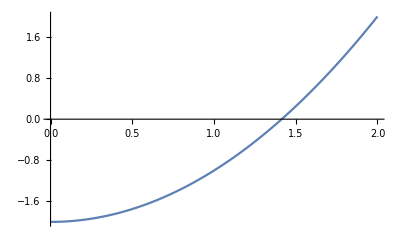

```mathematica
f[x_]:=x^2-2;
p[0]=1.5;
Do[p[n+1]=N[p[n]-f[p[n]]/f'[p[n]]],{n,0,5}]
Print["n","p[n]"]
TableForm[Table[{n,p[n]},{n,0,5}]]
Plot[f[x],{x,0,2}]
```

```mathematica
FindRoot[f[x],{x,2}]
```

{0.→1.41421}

```mathematica
Example 2
Use newton rapson  method to evaluate the function f(x)= x^3-5*x+1
```

Set::write: Tag Real in (-0.78125)[0] is Protected.

Set::write: Tag Real in (-0.78125)[1] is Protected.

Set::write: Tag Real in (-0.78125)[2] is Protected.

Set::write: Tag Real in (-0.78125)[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

np[n]

0 | (-0.78125)[0]
1 | (-0.78125)[1]
2 | (-0.78125)[2]
3 | (-0.78125)[3]
4 | (-0.78125)[4]
5 | (-0.78125)[5]
6 | (-0.78125)[6]
7 | (-0.78125)[7]

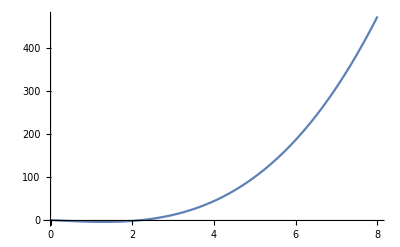

```mathematica
f[x_]:=x^3-5*x+1;
p[0]=1.5;
Do[p[n+1]=N[p[n]-f[p[n]]/f'[p[n]]],{n,0,7}]
Print["n","p[n]"]
TableForm[Table[{n,p[n]},{n,0,7}]]
Plot[f[x],{x,0,8}]
```

```mathematica
FindRoot[f[x],{x,6}]
```

{0.→2.12842}

```mathematica
Example 3
Use newton rapson  method to evaluate the function  f(x)=x^3-7*x+2
```

Set::write: Tag Real in (-0.78125)[0] is Protected.

Set::write: Tag Real in (-0.78125)[1] is Protected.

Set::write: Tag Real in (-0.78125)[2] is Protected.

Set::write: Tag Real in (-0.78125)[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

np[n]

0 | (-0.78125)[0]
1 | (-0.78125)[1]
2 | (-0.78125)[2]
3 | (-0.78125)[3]
4 | (-0.78125)[4]
5 | (-0.78125)[5]

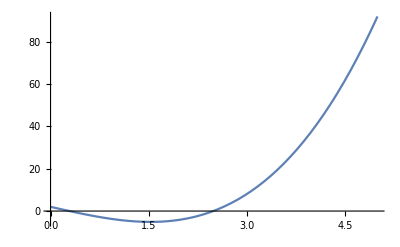

```mathematica
f[x_]:=x^3-7*x+2;
p[0]=2.5;
Do[p[n+1]=N[p[n]-f[p[n]]/f'[p[n]]],{n,0,5}]
Print["n","p[n]"]
TableForm[Table[{n,p[n]},{n,0,5}]]
Plot[f[x],{x,0,5}]
```

```mathematica
FindRoot[f[x],{x,6}]
```

{0.→2.48929}